```mathematica
mult[n1_,n2_]:=(
width=8;
divisor=2^width;
n1re=Mod[n1,divisor];
n1im=(n1-n1re)/divisor;
n2re=Mod[n2,divisor];
n2im=(n2-n2re)/divisor;
n1c=n1re+ⅈ*n1im;
n2c=n2re+ⅈ*n2im;
Table[BaseForm[n,16],{n,{n1im,n1re,n2im,n2re}}];
c=n1c*n2c;
BaseForm[Re[c],16]
);
mult[16^^7d7e,16^^f8fa]
```

(1f4)_16

```mathematica
72*1024/32/2
```

1152

```mathematica
2^9
```

512

```mathematica
72*1024/16/2
```

2304

```mathematica
2^11
```

2048

```mathematica
72*1000/16
```

4500

```mathematica
2^9
```

512

```mathematica
(* we have decided on a 16 bit representation with 512 samples (so that logN is an odd number). Time to do some frequency calculations to make sure we get good audible range response. *)
```

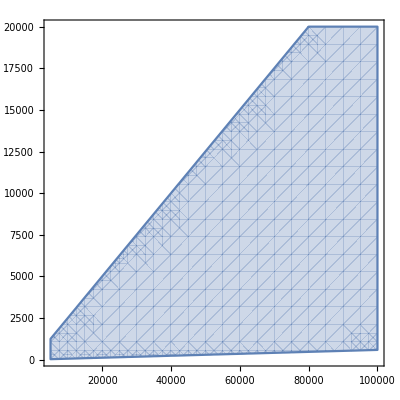

234.375<of<10000.

156.25<of<20000.

```mathematica
samplesize=512;
cyclesin[samplespeed_,observingfreq_]:=(
sampleduration=samplesize/samplespeed;
sampleduration/(1/observingfreq)
);
(* audible range: 20 to 20,000 Hz *)
(* a good cyclesin: 3 < cyclesin < (samplesize/4) *)
(* an acceptable cyclesin: 2 < cyclesin < (samplesize/2) *)
goodperf=3<cyclesin[ss, of]<(samplesize/4);
acceptableperf=2<cyclesin[ss, of]<(samplesize/2);
RegionPlot[goodperf,{ss,5000,100000},{of,20,20000}]
(*RegionPlot[acceptableperf,{ss,5000,100000},{of,20,20000}]*)
Reduce[goodperf/.ss->40000]//N
Reduce[acceptableperf/.ss->40000]//N
```